```mathematica
(*所使用的方程为  e^(-π Subscript[R, 垂直]/Subscript[R, s])+e^(-π Subscript[R, 平行/Subscript[R, s]])=1*)
```

```mathematica
Clear["Gloal`*"];
vertical`data=Import["C:\\Users\\aoubl\\Desktop\\CrO2 Fit data\\rho-b.xlsx","EmptyField"->"Empty"];
vertical`data=vertical`data[[1]];
vertical`data=Transpose@vertical`data;
T`data=vertical`data[[1]];

rho`vertical`data=vertical`data[[2]];




horizontal`data=Import["C:\\Users\\aoubl\\Desktop\\CrO2 Fit data\\rho-c.xlsx","EmptyField"->"Empty"];
horizontal`data=horizontal`data[[1]];
horizontal`data=Transpose@horizontal`data;
rho`horizontal`data=horizontal`data[[2]];
film`rho`data={};
Do[rho=y/.Flatten@NSolve[Exp[-π*rho`vertical`data[[i]]/y]+Exp[-π*rho`horizontal`data[[i]]/y]==1,y,Reals];AppendTo[film`rho`data,{T`data[[i]],rho}],{i,Length@rho`vertical`data}]
```

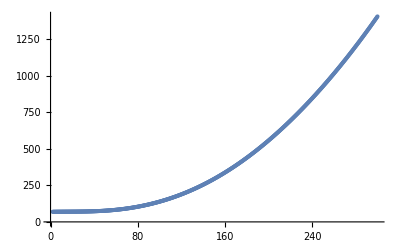

```mathematica
ListPlot@film`rho`data
```

```mathematica
y/.Flatten@NSolve[Exp[-π*rho`vertical`data[[1]]/y]+Exp[-π*rho`horizontal`data[[1]]/y]==1,y,Reals]
```

68.9058